# 01

Using Polar Plot

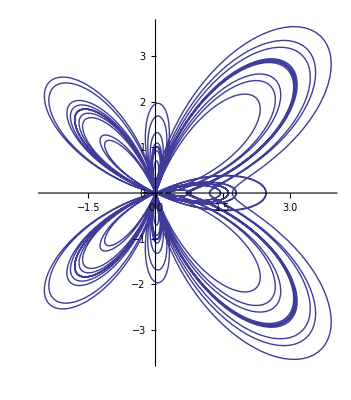

Using Parametric Plot

-Graphics-

Using Parametric Plot Formula

-Graphics-

```mathematica
w1=ⅇ^Cos[t]-2*Cos[4*t]+Sin[t/12]^5;Print["Using Polar Plot"]
PolarPlot[w1,{t,0,24*Pi}]

w2=CoordinateTransform[ "Polar" -> "Cartesian",{w1,t}];
Print["Using Parametric Plot"]
ParametricPlot[w2,{t,0,24Pi}]
Print["Using Parametric Plot Formula"]
ParametricPlot[{w1*Cos[t],w1*Sin[t]},{t,0,24Pi}]
```

# 02

-Graphics3D-

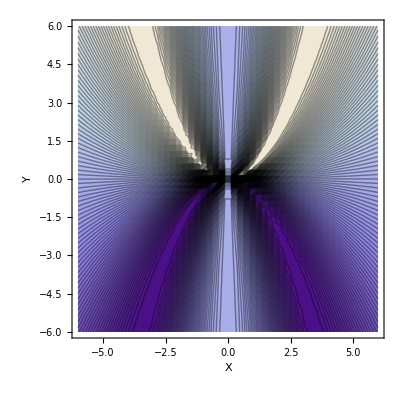

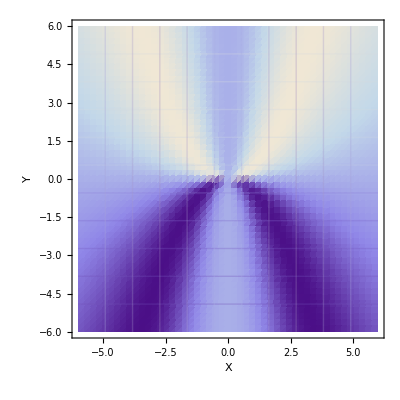

```mathematica
f[x_,y_]:=x^2*y/(x^4+4*y^2)
Plot3D[f[x,y],{x,-6,6},{y,-6,6}, AxesLabel->{X,Y,Z},PlotPoints->50,Mesh->10,MaxRecursion->0,PlotStyle->{Orange,Dashed,Thick},ColorFunction->"BlueGreenYellow"]
ContourPlot[f[x,y],{x,-6,6},{y,-6,6}, AxesLabel->{X,Y,Z},PlotPoints->50,Mesh->10,MaxRecursion->0,Contours->100,MeshStyle->All]
DensityPlot[f[x,y],{x,-6,6},{y,-6,6}, AxesLabel->{X,Y,Z},PlotPoints->50,Mesh->10,MaxRecursion->0]
```

# 03

```mathematica
Clear[All]
n={3,1,5};r={x,y,z};r0={-2,1,3};
eq3=Solve[n.(r-r0)==0,z][[1,1,2]]
Plot3D[eq3,{x,-2,2},{y,-2,2},ColorFunction->"Rainbow"]
```

1/5 (10-3 x-y)

-Graphics3D-

# 04

```mathematica
Clear[All]
eq1=(x/4)^2+(y/2)^2+z^2==1
Print["Answer (i):"]
ParametricPlot3D[{4*Cos[t]Cos[r],2*Cos[t]Sin[r],Sin[t]},{t,-Pi/2,Pi/2},{r,-Pi,Pi}]
Print["Answer (i):"]
ContourPlot3D[(x/4)^2+(y/2)^2+z^2==1,{x,-4,4},{y,-4,4},{z,-4,4},BoxRatios->{1,1,1},Mesh->10]
```

x^2/16+y^2/4+z^2==1

Answer (i):

-Graphics3D-

Answer (i):

-Graphics3D-

# 05

(i)Plot function

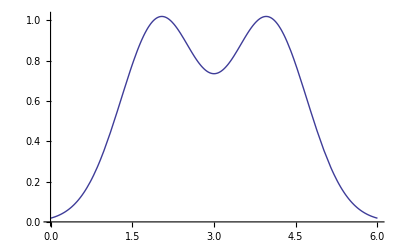

(ii) The volume of the solid under revolving condition is=8.76132

(iii) RevolutionPlot3D

-Graphics3D-

ParametricPlot3D:

-Graphics3D-

(iv) Volume under revolving condition:=61.5638

(v) ParametricPlot3D:

-Graphics3D-

RevolutionPlot3D:

-Graphics3D-

```mathematica
f[x_]:=ⅇ^(-(x-2)^2)+ⅇ^(-(x-4)^2)
Print["(i)Plot function"]
Plot[f[x],{x,0,6}]

v1=Integrate[Pi*f[x]^2,{x,1,5}]//N;
Print["(ii) The volume of the solid under revolving condition is=",v1]

Print["(iii) RevolutionPlot3D"]
RevolutionPlot3D[f[x],{x,1,5},RevolutionAxis->{1,0,0}]
Print["ParametricPlot3D:"]
ParametricPlot3D[{f[x]*Cos[t],f[x]*Sin[t],x},{x,1,5},{t,0,2Pi}]

v2=Integrate[Pi*f[x]*2*x,{x,1,5}]//N;
Print["(iv) Volume under revolving condition:=",v2]

Print["(v) ParametricPlot3D:"]
ParametricPlot3D[{x*Cos[t],x*Sin[t],f[x]},{x,1,5},{t,0,2Pi},BoxRatios->{4,4,1}]
(*Age j x chilo she ekhon y hoye jabe i.e. x≤≥f[x]*)
Print["RevolutionPlot3D:"]
RevolutionPlot3D[f[x],{x,1,5},RevolutionAxis->{0,0,1}]
```